```mathematica
(*Mathematica*)
```

```mathematica
gm0=1.13060005
```

1.1306

```mathematica
N[gm0]
```

1.1306

```mathematica
gm1=1.1307100509999999
```

1.13071

```mathematica
gm=Table[(1-p)*(gm0)+p*gm1,{p,0.1,1.1,1/200}];
```

```mathematica
Length[gm]
N[gm]
```

201

{1.13061,1.13061,1.13061,1.13061,1.13061,1.13061,1.13061,1.13061,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13062,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13063,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13064,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13065,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13066,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13067,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13068,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.13069,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.1307,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13071,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072,1.13072}

```mathematica
f[z_]:=-z*(ⅇ^(2 ⅈ π gm[[i]])/(√(-1+ⅇ^(2 ⅈ π gm[[i]]))))+z^2
```

```mathematica
(*v=JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001];*)
```

```mathematica
tm=ParallelTable[{i,Timing[ListPlot[JuliaSetPoints[f[z],z,"ClosenessTolerance"->0.001],ImageSize->{1920,1040},PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,DisplayFunction->False];]},{i,Length[gm]}]
```

{{1,{145.839,Null}},{2,{145.325,Null}},{3,{165.949,Null}},{4,{165.784,Null}},{5,{146.265,Null}},{6,{156.956,Null}},{7,{146.27,Null}},{8,{149.155,Null}},{9,{154.513,Null}},{10,{153.899,Null}},{11,{156.751,Null}},{12,{157.925,Null}},{13,{159.169,Null}},{14,{154.869,Null}},{15,{154.824,Null}},{16,{154.288,Null}},{17,{153.98,Null}},{18,{155.703,Null}},{19,{139.009,Null}},{20,{144.123,Null}},{21,{143.472,Null}},{22,{142.382,Null}},{23,{144.182,Null}},{24,{147.368,Null}},{25,{145.909,Null}},{26,{144.957,Null}},{27,{135.151,Null}},{28,{141.182,Null}},{29,{121.858,Null}},{30,{107.101,Null}},{31,{120.746,Null}},{32,{123.966,Null}},{33,{127.681,Null}},{34,{127.871,Null}},{35,{142.21,Null}},{36,{125.676,Null}},{37,{132.342,Null}},{38,{131.079,Null}},{39,{135.776,Null}},{40,{121.317,Null}},{41,{124.425,Null}},{42,{118.974,Null}},{43,{116.75,Null}},{44,{114.535,Null}},{45,{118.45,Null}},{46,{124.038,Null}},{47,{123.567,Null}},{48,{122.631,Null}},{49,{147.766,Null}},{50,{137.527,Null}},{51,{137.998,Null}},{52,{143.091,Null}},{53,{160.257,Null}},{54,{159.671,Null}},{55,{128.65,Null}},{56,{131.293,Null}},{57,{132.098,Null}},{58,{134.564,Null}},{59,{139.33,Null}},{60,{138.516,Null}},{61,{139.216,Null}},{62,{156.724,Null}},{63,{137.632,Null}},{64,{139.349,Null}},{65,{199.911,Null}},{66,{211.682,Null}},{67,{223.621,Null}},{68,{197.712,Null}},{69,{159.442,Null}},{70,{165.254,Null}},{71,{163.77,Null}},{72,{163.43,Null}},{73,{150.569,Null}},{74,{162.73,Null}},{75,{174.817,Null}},{76,{175.892,Null}},{77,{156.591,Null}},{78,{174.512,Null}},{79,{168.967,Null}},{80,{167.913,Null}},{81,{163.454,Null}},{82,{169.987,Null}},{83,{170.144,Null}},{84,{156.81,Null}},{85,{157.174,Null}},{86,{161.572,Null}},{87,{178.903,Null}},{88,{180.142,Null}},{89,{198.238,Null}},{90,{158.871,Null}},{91,{204.38,Null}},{92,{198.715,Null}},{93,{198.37,Null}},{94,{208.497,Null}},{95,{190.645,Null}},{96,{191.564,Null}},{97,{190.694,Null}},{98,{194.926,Null}},{99,{191.972,Null}},{100,{164.562,Null}},{101,{116.556,Null}},{102,{117.829,Null}},{103,{117.82,Null}},{104,{114.557,Null}},{105,{114.925,Null}},{106,{114.198,Null}},{107,{115.804,Null}},{108,{170.419,Null}},{109,{171.218,Null}},{110,{174.92,Null}},{111,{173.565,Null}},{112,{171.434,Null}},{113,{190.048,Null}},{114,{187.866,Null}},{115,{193.658,Null}},{116,{185.772,Null}},{117,{182.682,Null}},{118,{193.486,Null}},{119,{175.89,Null}},{120,{155.547,Null}},{121,{155.845,Null}},{122,{185.106,Null}},{123,{194.88,Null}},{124,{194.377,Null}},{125,{188.056,Null}},{126,{187.986,Null}},{127,{188.125,Null}},{128,{182.188,Null}},{129,{187.697,Null}},{130,{123.028,Null}},{131,{121.63,Null}},{132,{120.967,Null}},{133,{119.993,Null}},{134,{119.853,Null}},{135,{189.204,Null}},{136,{173.824,Null}},{137,{170.237,Null}},{138,{169.271,Null}},{139,{140.978,Null}},{140,{144.557,Null}},{141,{143.652,Null}},{142,{148.7,Null}},{143,{145.48,Null}},{144,{142.616,Null}},{145,{149.259,Null}},{146,{144.712,Null}},{147,{145.423,Null}},{148,{169.071,Null}},{149,{165.341,Null}},{150,{165.568,Null}},{151,{184.84,Null}},{152,{144.326,Null}},{153,{147.048,Null}},{154,{183.794,Null}},{155,{167.565,Null}},{156,{168.57,Null}},{157,{191.3,Null}},{158,{186.275,Null}},{159,{187.281,Null}},{160,{189.117,Null}},{161,{186.221,Null}},{162,{177.368,Null}},{163,{148.385,Null}},{164,{150.233,Null}},{165,{171.801,Null}},{166,{176.235,Null}},{167,{176.4,Null}},{168,{177.351,Null}},{169,{176.704,Null}},{170,{177.507,Null}},{171,{181.648,Null}},{172,{183.126,Null}},{173,{182.611,Null}},{174,{157.028,Null}},{175,{153.537,Null}},{176,{154.824,Null}},{177,{164.787,Null}},{178,{164.762,Null}},{179,{164.988,Null}},{180,{144.098,Null}},{181,{144.969,Null}},{182,{144.933,Null}},{183,{148.324,Null}},{184,{149.028,Null}},{185,{150.256,Null}},{186,{152.35,Null}},{187,{148.393,Null}},{188,{147.203,Null}},{189,{164.144,Null}},{190,{159.477,Null}},{191,{151.232,Null}},{192,{147.137,Null}},{193,{149.723,Null}},{194,{166.148,Null}},{195,{165.111,Null}},{196,{169.162,Null}},{197,{170.022,Null}},{198,{114.068,Null}},{199,{116.256,Null}},{200,{118.781,Null}},{201,{164.397,Null}}}

```mathematica
lt=ParallelTable[If[tm[[i,2,1]]>20,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]
```

{{1,145.839,1.13061},{2,145.325,1.13061},{3,165.949,1.13061},{4,165.784,1.13061},{5,146.265,1.13061},{6,156.956,1.13061},{7,146.27,1.13061},{8,149.155,1.13061},{9,154.513,1.13062},{10,153.899,1.13062},{11,156.751,1.13062},{12,157.925,1.13062},{13,159.169,1.13062},{14,154.869,1.13062},{15,154.824,1.13062},{16,154.288,1.13062},{17,153.98,1.13062},{18,155.703,1.13062},{19,139.009,1.13062},{20,144.123,1.13062},{21,143.472,1.13062},{22,142.382,1.13062},{23,144.182,1.13062},{24,147.368,1.13062},{25,145.909,1.13062},{26,144.957,1.13062},{27,135.151,1.13063},{28,141.182,1.13063},{29,121.858,1.13063},{30,107.101,1.13063},{31,120.746,1.13063},{32,123.966,1.13063},{33,127.681,1.13063},{34,127.871,1.13063},{35,142.21,1.13063},{36,125.676,1.13063},{37,132.342,1.13063},{38,131.079,1.13063},{39,135.776,1.13063},{40,121.317,1.13063},{41,124.425,1.13063},{42,118.974,1.13063},{43,116.75,1.13063},{44,114.535,1.13063},{45,118.45,1.13064},{46,124.038,1.13064},{47,123.567,1.13064},{48,122.631,1.13064},{49,147.766,1.13064},{50,137.527,1.13064},{51,137.998,1.13064},{52,143.091,1.13064},{53,160.257,1.13064},{54,159.671,1.13064},{55,128.65,1.13064},{56,131.293,1.13064},{57,132.098,1.13064},{58,134.564,1.13064},{59,139.33,1.13064},{60,138.516,1.13064},{61,139.216,1.13064},{62,156.724,1.13064},{63,137.632,1.13065},{64,139.349,1.13065},{65,199.911,1.13065},{66,211.682,1.13065},{67,223.621,1.13065},{68,197.712,1.13065},{69,159.442,1.13065},{70,165.254,1.13065},{71,163.77,1.13065},{72,163.43,1.13065},{73,150.569,1.13065},{74,162.73,1.13065},{75,174.817,1.13065},{76,175.892,1.13065},{77,156.591,1.13065},{78,174.512,1.13065},{79,168.967,1.13065},{80,167.913,1.13065},{81,163.454,1.13066},{82,169.987,1.13066},{83,170.144,1.13066},{84,156.81,1.13066},{85,157.174,1.13066},{86,161.572,1.13066},{87,178.903,1.13066},{88,180.142,1.13066},{89,198.238,1.13066},{90,158.871,1.13066},{91,204.38,1.13066},{92,198.715,1.13066},{93,198.37,1.13066},{94,208.497,1.13066},{95,190.645,1.13066},{96,191.564,1.13066},{97,190.694,1.13066},{98,194.926,1.13066},{99,191.972,1.13066},{100,164.562,1.13067},{101,116.556,1.13067},{102,117.829,1.13067},{103,117.82,1.13067},{104,114.557,1.13067},{105,114.925,1.13067},{106,114.198,1.13067},{107,115.804,1.13067},{108,170.419,1.13067},{109,171.218,1.13067},{110,174.92,1.13067},{111,173.565,1.13067},{112,171.434,1.13067},{113,190.048,1.13067},{114,187.866,1.13067},{115,193.658,1.13067},{116,185.772,1.13067},{117,182.682,1.13067},{118,193.486,1.13068},{119,175.89,1.13068},{120,155.547,1.13068},{121,155.845,1.13068},{122,185.106,1.13068},{123,194.88,1.13068},{124,194.377,1.13068},{125,188.056,1.13068},{126,187.986,1.13068},{127,188.125,1.13068},{128,182.188,1.13068},{129,187.697,1.13068},{130,123.028,1.13068},{131,121.63,1.13068},{132,120.967,1.13068},{133,119.993,1.13068},{134,119.853,1.13068},{135,189.204,1.13068},{136,173.824,1.13069},{137,170.237,1.13069},{138,169.271,1.13069},{139,140.978,1.13069},{140,144.557,1.13069},{141,143.652,1.13069},{142,148.7,1.13069},{143,145.48,1.13069},{144,142.616,1.13069},{145,149.259,1.13069},{146,144.712,1.13069},{147,145.423,1.13069},{148,169.071,1.13069},{149,165.341,1.13069},{150,165.568,1.13069},{151,184.84,1.13069},{152,144.326,1.13069},{153,147.048,1.13069},{154,183.794,1.1307},{155,167.565,1.1307},{156,168.57,1.1307},{157,191.3,1.1307},{158,186.275,1.1307},{159,187.281,1.1307},{160,189.117,1.1307},{161,186.221,1.1307},{162,177.368,1.1307},{163,148.385,1.1307},{164,150.233,1.1307},{165,171.801,1.1307},{166,176.235,1.1307},{167,176.4,1.1307},{168,177.351,1.1307},{169,176.704,1.1307},{170,177.507,1.1307},{171,181.648,1.1307},{172,183.126,1.13071},{173,182.611,1.13071},{174,157.028,1.13071},{175,153.537,1.13071},{176,154.824,1.13071},{177,164.787,1.13071},{178,164.762,1.13071},{179,164.988,1.13071},{180,144.098,1.13071},{181,144.969,1.13071},{182,144.933,1.13071},{183,148.324,1.13071},{184,149.028,1.13071},{185,150.256,1.13071},{186,152.35,1.13071},{187,148.393,1.13071},{188,147.203,1.13071},{189,164.144,1.13071},{190,159.477,1.13072},{191,151.232,1.13072},{192,147.137,1.13072},{193,149.723,1.13072},{194,166.148,1.13072},{195,165.111,1.13072},{196,169.162,1.13072},{197,170.022,1.13072},{198,114.068,1.13072},{199,116.256,1.13072},{200,118.781,1.13072},{201,164.397,1.13072}}

```mathematica
lt150=N[ParallelTable[If[tm[[i,2,1]]>100,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]]
```

{{1.,145.839,1.13061},{2.,145.325,1.13061},{3.,165.949,1.13061},{4.,165.784,1.13061},{5.,146.265,1.13061},{6.,156.956,1.13061},{7.,146.27,1.13061},{8.,149.155,1.13061},{9.,154.513,1.13062},{10.,153.899,1.13062},{11.,156.751,1.13062},{12.,157.925,1.13062},{13.,159.169,1.13062},{14.,154.869,1.13062},{15.,154.824,1.13062},{16.,154.288,1.13062},{17.,153.98,1.13062},{18.,155.703,1.13062},{19.,139.009,1.13062},{20.,144.123,1.13062},{21.,143.472,1.13062},{22.,142.382,1.13062},{23.,144.182,1.13062},{24.,147.368,1.13062},{25.,145.909,1.13062},{26.,144.957,1.13062},{27.,135.151,1.13063},{28.,141.182,1.13063},{29.,121.858,1.13063},{30.,107.101,1.13063},{31.,120.746,1.13063},{32.,123.966,1.13063},{33.,127.681,1.13063},{34.,127.871,1.13063},{35.,142.21,1.13063},{36.,125.676,1.13063},{37.,132.342,1.13063},{38.,131.079,1.13063},{39.,135.776,1.13063},{40.,121.317,1.13063},{41.,124.425,1.13063},{42.,118.974,1.13063},{43.,116.75,1.13063},{44.,114.535,1.13063},{45.,118.45,1.13064},{46.,124.038,1.13064},{47.,123.567,1.13064},{48.,122.631,1.13064},{49.,147.766,1.13064},{50.,137.527,1.13064},{51.,137.998,1.13064},{52.,143.091,1.13064},{53.,160.257,1.13064},{54.,159.671,1.13064},{55.,128.65,1.13064},{56.,131.293,1.13064},{57.,132.098,1.13064},{58.,134.564,1.13064},{59.,139.33,1.13064},{60.,138.516,1.13064},{61.,139.216,1.13064},{62.,156.724,1.13064},{63.,137.632,1.13065},{64.,139.349,1.13065},{65.,199.911,1.13065},{66.,211.682,1.13065},{67.,223.621,1.13065},{68.,197.712,1.13065},{69.,159.442,1.13065},{70.,165.254,1.13065},{71.,163.77,1.13065},{72.,163.43,1.13065},{73.,150.569,1.13065},{74.,162.73,1.13065},{75.,174.817,1.13065},{76.,175.892,1.13065},{77.,156.591,1.13065},{78.,174.512,1.13065},{79.,168.967,1.13065},{80.,167.913,1.13065},{81.,163.454,1.13066},{82.,169.987,1.13066},{83.,170.144,1.13066},{84.,156.81,1.13066},{85.,157.174,1.13066},{86.,161.572,1.13066},{87.,178.903,1.13066},{88.,180.142,1.13066},{89.,198.238,1.13066},{90.,158.871,1.13066},{91.,204.38,1.13066},{92.,198.715,1.13066},{93.,198.37,1.13066},{94.,208.497,1.13066},{95.,190.645,1.13066},{96.,191.564,1.13066},{97.,190.694,1.13066},{98.,194.926,1.13066},{99.,191.972,1.13066},{100.,164.562,1.13067},{101.,116.556,1.13067},{102.,117.829,1.13067},{103.,117.82,1.13067},{104.,114.557,1.13067},{105.,114.925,1.13067},{106.,114.198,1.13067},{107.,115.804,1.13067},{108.,170.419,1.13067},{109.,171.218,1.13067},{110.,174.92,1.13067},{111.,173.565,1.13067},{112.,171.434,1.13067},{113.,190.048,1.13067},{114.,187.866,1.13067},{115.,193.658,1.13067},{116.,185.772,1.13067},{117.,182.682,1.13067},{118.,193.486,1.13068},{119.,175.89,1.13068},{120.,155.547,1.13068},{121.,155.845,1.13068},{122.,185.106,1.13068},{123.,194.88,1.13068},{124.,194.377,1.13068},{125.,188.056,1.13068},{126.,187.986,1.13068},{127.,188.125,1.13068},{128.,182.188,1.13068},{129.,187.697,1.13068},{130.,123.028,1.13068},{131.,121.63,1.13068},{132.,120.967,1.13068},{133.,119.993,1.13068},{134.,119.853,1.13068},{135.,189.204,1.13068},{136.,173.824,1.13069},{137.,170.237,1.13069},{138.,169.271,1.13069},{139.,140.978,1.13069},{140.,144.557,1.13069},{141.,143.652,1.13069},{142.,148.7,1.13069},{143.,145.48,1.13069},{144.,142.616,1.13069},{145.,149.259,1.13069},{146.,144.712,1.13069},{147.,145.423,1.13069},{148.,169.071,1.13069},{149.,165.341,1.13069},{150.,165.568,1.13069},{151.,184.84,1.13069},{152.,144.326,1.13069},{153.,147.048,1.13069},{154.,183.794,1.1307},{155.,167.565,1.1307},{156.,168.57,1.1307},{157.,191.3,1.1307},{158.,186.275,1.1307},{159.,187.281,1.1307},{160.,189.117,1.1307},{161.,186.221,1.1307},{162.,177.368,1.1307},{163.,148.385,1.1307},{164.,150.233,1.1307},{165.,171.801,1.1307},{166.,176.235,1.1307},{167.,176.4,1.1307},{168.,177.351,1.1307},{169.,176.704,1.1307},{170.,177.507,1.1307},{171.,181.648,1.1307},{172.,183.126,1.13071},{173.,182.611,1.13071},{174.,157.028,1.13071},{175.,153.537,1.13071},{176.,154.824,1.13071},{177.,164.787,1.13071},{178.,164.762,1.13071},{179.,164.988,1.13071},{180.,144.098,1.13071},{181.,144.969,1.13071},{182.,144.933,1.13071},{183.,148.324,1.13071},{184.,149.028,1.13071},{185.,150.256,1.13071},{186.,152.35,1.13071},{187.,148.393,1.13071},{188.,147.203,1.13071},{189.,164.144,1.13071},{190.,159.477,1.13072},{191.,151.232,1.13072},{192.,147.137,1.13072},{193.,149.723,1.13072},{194.,166.148,1.13072},{195.,165.111,1.13072},{196.,169.162,1.13072},{197.,170.022,1.13072},{198.,114.068,1.13072},{199.,116.256,1.13072},{200.,118.781,1.13072},{201.,164.397,1.13072}}

```mathematica
lt200=N[ParallelTable[If[tm[[i,2,1]]>200,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]]
```

```mathematica
{{66.,211.681529,1.1306468004249999},{67.,223.620795,1.1306473504299999},{91.,204.380439,1.13066055055},{94.,208.497286,1.1306622005649998}}
```

```mathematica
(*All Timing results*)
```

```mathematica
lt0=Table[{gm[[i]],tm[[i,2,1]]},{i,Length[tm]}];
```

```mathematica
N[lt]
```

{{1.,145.839,1.13061},{2.,145.325,1.13061},{3.,165.949,1.13061},{4.,165.784,1.13061},{5.,146.265,1.13061},{6.,156.956,1.13061},{7.,146.27,1.13061},{8.,149.155,1.13061},{9.,154.513,1.13062},{10.,153.899,1.13062},{11.,156.751,1.13062},{12.,157.925,1.13062},{13.,159.169,1.13062},{14.,154.869,1.13062},{15.,154.824,1.13062},{16.,154.288,1.13062},{17.,153.98,1.13062},{18.,155.703,1.13062},{19.,139.009,1.13062},{20.,144.123,1.13062},{21.,143.472,1.13062},{22.,142.382,1.13062},{23.,144.182,1.13062},{24.,147.368,1.13062},{25.,145.909,1.13062},{26.,144.957,1.13062},{27.,135.151,1.13063},{28.,141.182,1.13063},{29.,121.858,1.13063},{30.,107.101,1.13063},{31.,120.746,1.13063},{32.,123.966,1.13063},{33.,127.681,1.13063},{34.,127.871,1.13063},{35.,142.21,1.13063},{36.,125.676,1.13063},{37.,132.342,1.13063},{38.,131.079,1.13063},{39.,135.776,1.13063},{40.,121.317,1.13063},{41.,124.425,1.13063},{42.,118.974,1.13063},{43.,116.75,1.13063},{44.,114.535,1.13063},{45.,118.45,1.13064},{46.,124.038,1.13064},{47.,123.567,1.13064},{48.,122.631,1.13064},{49.,147.766,1.13064},{50.,137.527,1.13064},{51.,137.998,1.13064},{52.,143.091,1.13064},{53.,160.257,1.13064},{54.,159.671,1.13064},{55.,128.65,1.13064},{56.,131.293,1.13064},{57.,132.098,1.13064},{58.,134.564,1.13064},{59.,139.33,1.13064},{60.,138.516,1.13064},{61.,139.216,1.13064},{62.,156.724,1.13064},{63.,137.632,1.13065},{64.,139.349,1.13065},{65.,199.911,1.13065},{66.,211.682,1.13065},{67.,223.621,1.13065},{68.,197.712,1.13065},{69.,159.442,1.13065},{70.,165.254,1.13065},{71.,163.77,1.13065},{72.,163.43,1.13065},{73.,150.569,1.13065},{74.,162.73,1.13065},{75.,174.817,1.13065},{76.,175.892,1.13065},{77.,156.591,1.13065},{78.,174.512,1.13065},{79.,168.967,1.13065},{80.,167.913,1.13065},{81.,163.454,1.13066},{82.,169.987,1.13066},{83.,170.144,1.13066},{84.,156.81,1.13066},{85.,157.174,1.13066},{86.,161.572,1.13066},{87.,178.903,1.13066},{88.,180.142,1.13066},{89.,198.238,1.13066},{90.,158.871,1.13066},{91.,204.38,1.13066},{92.,198.715,1.13066},{93.,198.37,1.13066},{94.,208.497,1.13066},{95.,190.645,1.13066},{96.,191.564,1.13066},{97.,190.694,1.13066},{98.,194.926,1.13066},{99.,191.972,1.13066},{100.,164.562,1.13067},{101.,116.556,1.13067},{102.,117.829,1.13067},{103.,117.82,1.13067},{104.,114.557,1.13067},{105.,114.925,1.13067},{106.,114.198,1.13067},{107.,115.804,1.13067},{108.,170.419,1.13067},{109.,171.218,1.13067},{110.,174.92,1.13067},{111.,173.565,1.13067},{112.,171.434,1.13067},{113.,190.048,1.13067},{114.,187.866,1.13067},{115.,193.658,1.13067},{116.,185.772,1.13067},{117.,182.682,1.13067},{118.,193.486,1.13068},{119.,175.89,1.13068},{120.,155.547,1.13068},{121.,155.845,1.13068},{122.,185.106,1.13068},{123.,194.88,1.13068},{124.,194.377,1.13068},{125.,188.056,1.13068},{126.,187.986,1.13068},{127.,188.125,1.13068},{128.,182.188,1.13068},{129.,187.697,1.13068},{130.,123.028,1.13068},{131.,121.63,1.13068},{132.,120.967,1.13068},{133.,119.993,1.13068},{134.,119.853,1.13068},{135.,189.204,1.13068},{136.,173.824,1.13069},{137.,170.237,1.13069},{138.,169.271,1.13069},{139.,140.978,1.13069},{140.,144.557,1.13069},{141.,143.652,1.13069},{142.,148.7,1.13069},{143.,145.48,1.13069},{144.,142.616,1.13069},{145.,149.259,1.13069},{146.,144.712,1.13069},{147.,145.423,1.13069},{148.,169.071,1.13069},{149.,165.341,1.13069},{150.,165.568,1.13069},{151.,184.84,1.13069},{152.,144.326,1.13069},{153.,147.048,1.13069},{154.,183.794,1.1307},{155.,167.565,1.1307},{156.,168.57,1.1307},{157.,191.3,1.1307},{158.,186.275,1.1307},{159.,187.281,1.1307},{160.,189.117,1.1307},{161.,186.221,1.1307},{162.,177.368,1.1307},{163.,148.385,1.1307},{164.,150.233,1.1307},{165.,171.801,1.1307},{166.,176.235,1.1307},{167.,176.4,1.1307},{168.,177.351,1.1307},{169.,176.704,1.1307},{170.,177.507,1.1307},{171.,181.648,1.1307},{172.,183.126,1.13071},{173.,182.611,1.13071},{174.,157.028,1.13071},{175.,153.537,1.13071},{176.,154.824,1.13071},{177.,164.787,1.13071},{178.,164.762,1.13071},{179.,164.988,1.13071},{180.,144.098,1.13071},{181.,144.969,1.13071},{182.,144.933,1.13071},{183.,148.324,1.13071},{184.,149.028,1.13071},{185.,150.256,1.13071},{186.,152.35,1.13071},{187.,148.393,1.13071},{188.,147.203,1.13071},{189.,164.144,1.13071},{190.,159.477,1.13072},{191.,151.232,1.13072},{192.,147.137,1.13072},{193.,149.723,1.13072},{194.,166.148,1.13072},{195.,165.111,1.13072},{196.,169.162,1.13072},{197.,170.022,1.13072},{198.,114.068,1.13072},{199.,116.256,1.13072},{200.,118.781,1.13072},{201.,164.397,1.13072}}

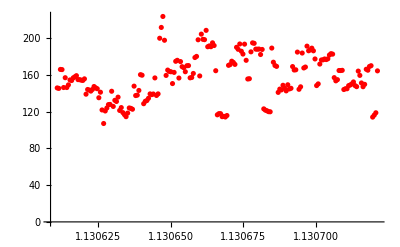

```mathematica
ListPlot[lt0,PlotStyle->Red,ImageSize->Full,PlotRange->All]
```

```mathematica
ListPointPlot3D[lt200,PlotStyle->Red,ImageSize->Full]
```

-Graphics3D-

```mathematica
st=ParallelTable[If[tm[[i,2,1]]<1,{i,tm[[i,2,1]],gm[[i]]},Nothing],{i,Length[tm]}]
```

{}

```mathematica
(*end*)
```